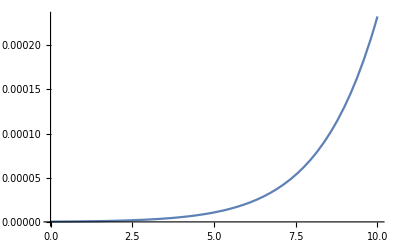

```mathematica
epsilon=0.03;
sigma=1/5;
prext=0.5*Erfc[(1-numpreds*epsilon)/(sigma*Sqrt[2])];
Plot[prext,{numpreds,0,10}]
```

```mathematica
Remove[epsilon];
Remove[sigma];
Remove[prext];
Solve[prext==0.5*Erfc[(1-numpreds*epsilon)/(sigma*Sqtwo)],numpreds]
```

{{numpreds→1/epsilon(1.-1. sigma Sqtwo InverseErfc[2. prext])}}

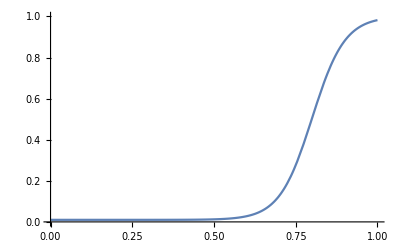

```mathematica
Plot[pb+(1-pb)1/(1+Exp[-k*(x-0.8)])/.{k->20,pb->0.01},{x,0,1},PlotRange->{0,1}]
```

```mathematica
Limit[pb+(1-pb)1/(1+Exp[-k*(x-0.8)]),k->Infinity]
```

ConditionalExpression[1.,pb∈ℝ&&5. x>4.]

```mathematica
extfunc=CDF[BetaDistribution[a,b],x]
```

Piecewise[{{BetaRegularized[x,a,b], 0<x<1}, {1, x≥1}, {0, True}}]

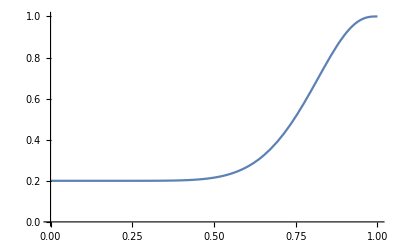

```mathematica
Plot[0.2+(1-0.2)*extfunc/.{a->10,b->3},{x,0,1},PlotRange->{0,1}]
```

```mathematica
Probability[x==0.5,x\[Distributed] CDF[BetaDistribution[a,b],x]]
```

Probability[x==0.5,x\[Distributed]Piecewise[{{BetaRegularized[x,a,b], 0<x<1}, {1, x≥1}, {0, True}}]]

```mathematica
Solve[BetaRegularized[x,a,6]==0.5,a]
```

Solve[BetaRegularized[x,a,6]==0.5,a]

```mathematica
Solve[BetaRegularized[0.5,10,a],a]
```

Solve[BetaRegularized[0.5,10,a],a]